```mathematica
maxiters=128;
```

```mathematica
init[n_]:={{1,11},{IntegerDigits[n,2,11],0}}
hist[n_, rule_]:=With[{min=Min[#[[All,1,2]],#[[1,1,2]]-11]-1},
Transpose[{
#-{0,min,0}&/@#[[All,1]],
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]
}]
]&@
Module[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
-10<=#[[1,3]]<=0,(* valid position *)
True,
MatchQ[#[[1,3]],1|-11], (* halt position *)
halt=True
]&
]
]&@
TuringMachine[rule,init[n],maxiters]
```

```mathematica
rules={3279,1285,3333,261,1447,1953,1969,3517,3246,3374,1507};
```

```mathematica
getcomponents[bits_Integer]:=ParallelTable[Transpose@Partition[
Flatten@Table[
With[{h=hist[n,r]},
{
RulePlot[
TuringMachine[r],
h,
Sequence[
Mesh->True,
MeshStyle->Directive[Thin,GrayLevel[0.15]],
ImageSize->{50,Automatic},
Frame->False
]
],
If[
h[[-1,1,3]]!=1,
-1,
FromDigits[h[[-1,2]],2]
]
}
], (* end With *)
{n,0,2^bits-1}
], (* end Table over n *)
2
] ,(* end Partition *) 
{r,rules}
];(* end Table over r *)
```

```mathematica
bits=5;
```

```mathematica
elems=getcomponents[bits];
```

```mathematica
Grid[
Flatten[elems,1],
Alignment->Top
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1 | 2 | 3 | 2 | 5 | 6 | 7 | 6 | 9 | 10 | 11 | 10 | 13 | 14 | 15 | 14 | 17 | 18 | 19 | 18 | 21 | 22 | 23 | 22 | 25 | 26 | 27 | 26 | 29 | 30 | 31 | 30
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 8 | 8 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 16 | 16 | 16 | 20 | 0 | 0 | 0 | 24 | 24 | 0 | 0 | 28 | 0 | 0 | 0
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 8 | 8 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 16 | 16 | 16 | 20 | 0 | 0 | 0 | 24 | 24 | 0 | 0 | 28 | 0 | 0 | 0
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 8 | 8 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 16 | 16 | 16 | 20 | 0 | 0 | 0 | 24 | 24 | 0 | 0 | 28 | 0 | 0 | 0
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 31 | 15 | 127 | 15 | 63 | 31 | 511 | 15 | 63 | 31 | 255 | 31 | 127 | 63 | 2047 | 23 | 63 | 31 | 255 | 31 | 127 | 63 | 1023 | 31 | 127 | 63 | 511 | 63 | 255 | 127 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 9 | 9 | 11 | 11 | 13 | 13 | 15 | 15 | 17 | 17 | 19 | 19 | 21 | 21 | 23 | 23 | 25 | 25 | 27 | 27 | 29 | 29 | 31 | 31
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 9 | 9 | 11 | 11 | 13 | 13 | 15 | 15 | 17 | 17 | 19 | 19 | 21 | 21 | 23 | 23 | 25 | 25 | 27 | 27 | 29 | 29 | 31 | 31
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 9 | 9 | 11 | 11 | 13 | 13 | 15 | 15 | 17 | 17 | 19 | 19 | 21 | 21 | 23 | 23 | 25 | 25 | 27 | 27 | 29 | 29 | 31 | 31
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-1 | -1 | -1 | 0 | -1 | 0 | 0 | 4 | -1 | 0 | 0 | 8 | 0 | 8 | 8 | 12 | -1 | 0 | 0 | 16 | 0 | 16 | 16 | 20 | 0 | 16 | 16 | 24 | 16 | 24 | 24 | 28
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-1 | -1 | -1 | 0 | -1 | 0 | 0 | 4 | -1 | 0 | 0 | 8 | 0 | 8 | 8 | 12 | -1 | 0 | 0 | 16 | 0 | 16 | 16 | 20 | 0 | 16 | 16 | 24 | 16 | 24 | 24 | 28
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1 | 7 | 3 | -1 | 5 | 15 | 7 | -1 | 9 | 15 | 11 | 63 | 13 | 31 | 15 | -1 | 17 | 23 | 19 | -1 | 21 | 31 | 23 | 255 | 25 | 31 | 27 | -1 | 29 | 63 | 31 | -1

```mathematica
eqlgroups=ParallelMap[First,GatherBy[Transpose[{rules,elems[[All,2]]}],#[[2]]&],{2}]
```

{{3279},{1285,3333,261},{1447},{1953,1969,3517},{3246,3374},{1507}}

```mathematica
ht[rule_,bits_]:=Table[
Module[{t=0,max=50+2^(Log[2,n]+1)},
NestWhile[
(t++;TuringMachine[rule,#])&,
{{1,bits,0},{IntegerDigits[n,2,bits],0}},
#[[1,3]]<=0&,(* stop when dx > 0, or when x >= 10 *)
1,
max
];
If[t==max,0,t]
],
{n,0,2^bits-1}
]
```

```mathematica
accumulateApply=ResourceFunction["AccumulateApply"];
```

```mathematica
halttimes=ParallelMap[{#,ht[#,bits]}&,eqlgroups,{2}];
```

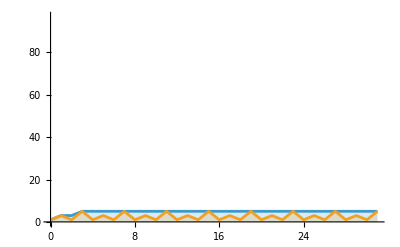
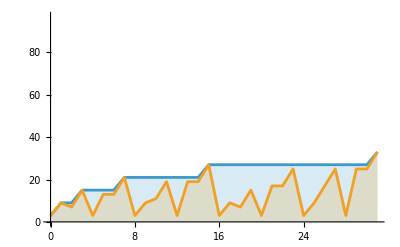
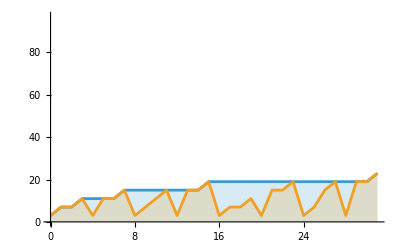
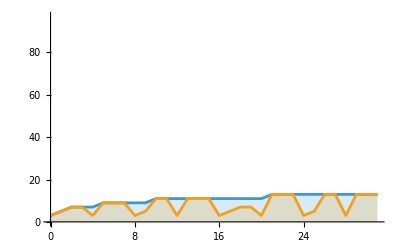
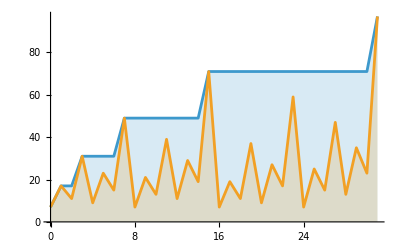
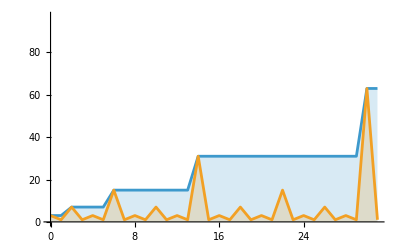
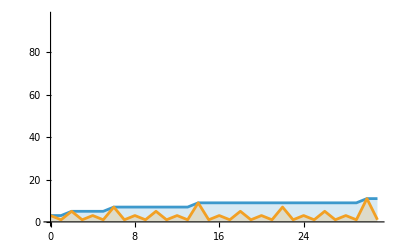
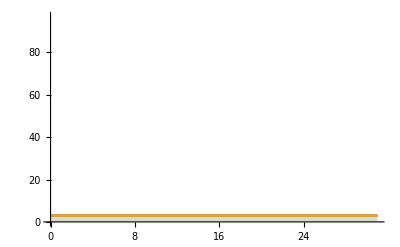
3279 | -Graphics- | 5{5,5,0}
1285 | -Graphics- | 33
3333 | -Graphics- | 23
261 | -Graphics- | 13{13,33,20}
1447 | -Graphics- | 97{97,97,0}
1953 | -Graphics- | 63
1969 | -Graphics- | 11
3517 | -Graphics- | 3{3,63,60}
3246 | -Graphics- | 9
3374 | -Graphics- | 15{9,15,6}
1507 | -Graphics- | 37{37,37,0}

```mathematica
Column[
With[{
row=Reap[With[{pfxmax=accumulateApply[Max,#[[2]]]},{
#[[1]],
ListPlot[
{pfxmax,#[[2]]},
DataRange->{0,2^bits-1},
PlotRange->{{0,2^bits-1},{0,Max[Flatten@halttimes[[All,All,2]]]}},
Filling->Axis,
Joined->True
],
Sow[pfxmax[[-1]]]
}
]&/@#](* end With *)
},(* end With init *)
Row[
With[{minmax=MinMax@row[[2]]},
{
Grid[row[[1]],Spacings->{2, 1},Frame->True],
Spacer[20],
{minmax[[1]],minmax[[2]],minmax[[2]]-minmax[[1]]}
}
]
](* end Row *)
]&/@halttimes,(* end With *)
Left,
0
](* end Column *)
```